Mathematica connection to NI-Data Acquisition (DAQ) cards

Banerjee Suman

Johnson Ian

Jawaharlal Nehru Centre for Advanced Scientific Research, Bangalore, India.

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: I have controlled hardware devices through serial ports, GPIB ports, USB ports using SerialRead/Write and NI-VISA from Mathematica. Here in WSS17 I wanted to control NI-DAQ cards using Mathematica. Through all these device communication protocols, large number of devices can be controlled which enables me to run my experiments efficiently using Mathematica.

SUMMARY OF WORK: DAQ cards are used for efficient measurements as they are compact and occupy less space than traditional devices. NI-DAQmx is an efficient driver to control NI-DAQ cards. In WSS17, I developed “DAQmxLink”, which controls NI-DAQ cards through NETLink.

RESULTS AND FUTURE  WORK: I have successfully controlled NI-USB-6000 DAQ cards using Mathematica through NETLink.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

-Graphics-

## NI - DAQ - Test

```mathematica
usb6000 = DeviceOpen["DAQmx"]
```

-Graphics-

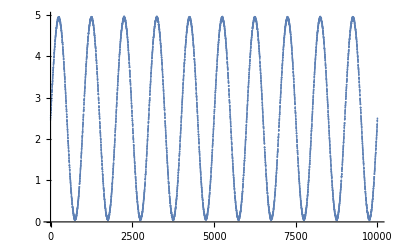

```mathematica
ListPlot[DeviceReadBuffer[usb6000,10000,"source"]]
```

```mathematica
Table[DeviceRead[usb6000],{i,1,10}]
```

{{2.46214},{2.4768},{2.49145},{2.50611},{2.52076},{2.53542},{2.55007},{2.56473},{2.58427},{2.59893}}

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Provide one of:

Link to the GitHub

Explicit code

NI-DAQ-6000

### Installation

```mathematica
<<NETLink`;
InstallNET[];
NationalInstruments$DAQmx = LoadNETAssembly["NationalInstruments.DAQmx","C:\\Program Files (x86)\\National Instruments\\MeasurementStudioVS2010\\DotNET\\Assemblies\\Current\\"];
NETAssembly["NationalInstruments.DAQmx",5];
```

### Device Framework

```mathematica
devOpen[iHandle_]:=Module[
{},
task = NETNew["NationalInstruments.DAQmx.Task"];
termConfig = NETNew["NationalInstruments.DAQmx.AITerminalConfiguration"]@Rse;
aiVolts = NETNew["NationalInstruments.DAQmx.AIVoltageUnits"]@Volts;
task@AIChannels@CreateVoltageChannel[
"Dev1/ai0"(*"Dev1/ai0"*),
"",
termConfig, 
0.0,
5.0,
aiVolts  
];
reader=NETNew["NationalInstruments.DAQmx.AnalogMultiChannelReader",task@Stream];
Return@reader
]

devRead[{iHandle_,dHandle_}]:=dHandle@ReadSingleSample[];
devReadBuffer[{iHandle_,dHandle_},samplenumber_Integer,source_String]:=Return @dHandle@ReadMultiSample[samplenumber];
(*Table[reader@ReadSingleSample[],{10}];
fulldata = reader@ReadMultiSample[1000];
Short[%]
Table[ListPlot[fulldata],{i,1,10}]*)
devReadBuffer[{iHandle_,dHandle_},All,source_String]:= 
devReadBuffer[{iHandle,dHandle},10000,source];
(*usb6000 = devOpen["Dev1/ai0"];
Table[devRead[usb6000],{i,1,10}]*)
```

```mathematica
DeviceFramework`DeviceClassRegister["DAQmx",
"OpenFunction"->devOpen,
(*"WriteFunction"-> K2400Write ,*)
"ReadFunction"-> devRead ,
"ReadBufferFunction"-> devReadBuffer 

(*"CloseFunction"->scopeClose*)
];
```

## NI - DAQ - Test

```mathematica
usb6000 = DeviceOpen["DAQmx"]
```

DeviceObject[…]

```mathematica
(*DeviceRead[usb6000]*)
```

```mathematica
ListPlot[DeviceReadBuffer[usb6000,10000,"source"]]
```

-Graphics-

```mathematica
Table[DeviceRead[usb6000],{i,1,10}]
```

{{2.46214},{2.4768},{2.49145},{2.50611},{2.52076},{2.53542},{2.55007},{2.56473},{2.58427},{2.59893}}

Written Content / Lesson Plans

Conclusions in Detail

I have successfully controlled NI - USB - 6000 DAQ cards using Mathematica through NETLink.

All Visualizations

```mathematica
ListPlot[DeviceReadBuffer[usb6000,10000,"source"]]
```

-Graphics-

```mathematica
Table[DeviceRead[usb6000],{i,1,10}]
```

{{2.46214},{2.4768},{2.49145},{2.50611},{2.52076},{2.53542},{2.55007},{2.56473},{2.58427},{2.59893}}

Data Sources Links/References

.NET classes

Future Directions

Clock

Trigger

Different DAQ hardwares

Background Info Links/References

Keywords

Provide keywords as items

<NI-DAQ control using Mathematica >

< DAQmx, Mathematica >

Other

Date

Last Modified: Monday, July 03, 2017

```mathematica
"Add Timestamp"
```